Quantum Information Scrambling on Kitaev Chain |

Setting up the modelpaclet:QuantumMob/QuantumPlaybook/tutorial/QuantumInformationScramblingOnKitaevChain#1828294694 | Simulation: Measurement effectspaclet:QuantumMob/QuantumPlaybook/tutorial/QuantumInformationScramblingOnKitaevChain#401426677
Simulation: Unitarypaclet:QuantumMob/QuantumPlaybook/tutorial/QuantumInformationScramblingOnKitaevChain#1558971231 |

We simulate the quantum information scrambling on the Kitaev chain in terms of the out-of-time-order correlator (OTOC).

BravyiScramblingCircuitpaclet:QuantumMob/Q3/ref/BravyiScramblingCircuitQuantumMob Package Symbol | Generates the main part of the quantum information scrambling circuit
BravyiScramblingSimulatepaclet:QuantumMob/Q3/ref/BravyiScramblingSimulateQuantumMob Package Symbol | Simulate the quantum information scrambling in fermionic Gaussian states

Quantum information scrambling in fermionic Gaussian states.

Make sure that Q3 is loaded:

```mathematica
Needs["QuantumMob`Q3`"]
```

Setting up the model

Set the number of fermion modes to consider:

```mathematica
$n=10;
```

Set the parameters:

```mathematica
μ=0.2;
t=Δ=1;
```

Directly construct the BdG Hamiltonian matrix (without using the fermion operator algebra as in the above section):

```mathematica
hrm=-μ*One[$n]-t*PlusTopple@One[{$n,$n},1];
del=-Δ*One[{$n,$n},1];
del=del-Transpose[del];
ham=NambuHermitian[{hrm,del}];
ham//ArrayShort
```

{(-0.2 | -1 | 0 | 0 | …
-1 | -0.2 | -1 | 0 | …
0 | -1 | -0.2 | -1 | …
0 | 0 | -1 | -0.2 | …
… | … | … | … | …),(0 | -1 | 0 | 0 | …
1 | 0 | -1 | 0 | …
0 | 1 | 0 | -1 | …
0 | 0 | 1 | 0 | …
… | … | … | … | …)}

The time interval for each unitary layer to operate:

```mathematica
$τ=3.;
```

Construct the single-particle unitary matrix:

```mathematica
uv=NambuUnitary@MatrixExp[-I*$τ*Normal[ham]]
```

NambuUnitary[…]

You can use the above unitary matrix in the Dirac spinor space (also known as the Nambu space). But it is slightly faster to first convert it to the equivalent matrix in the Majorana spinor space.:

```mathematica
wu=BravyiUnitary[uv] (* or wu=ToMajorana[uv] *)
```

BravyiUnitary[…]

Prepare an initial state. A half-filling is a common choice:

```mathematica
in=BravyiState[{1,0},$n]
```

BravyiState[…]

Set the depth of quantum circuit:

```mathematica
$T=20; (* must be an integer *)
```

Simulation: Unitary

```mathematica
SeedRandom[443];
```

```mathematica
Clear[otoc];
progress=p=0;
ProgressIndicator@Dynamic[progress]
Do[
otoc[k]=Table[
progress=++p/(($T+1)*($n-1));
BravyiScramblingSimulate[in,k,{wu,0},t,
"Samples"->{30,1}],
{t,0,$T}],
{k,1,$n}]
```

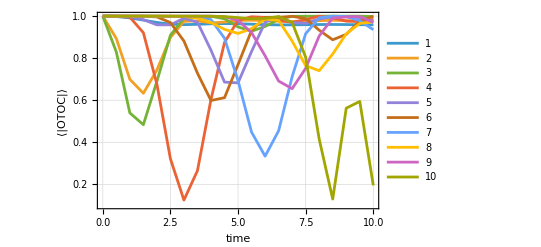

```mathematica
ListLinePlot[Array[otoc,$n],
DataRange->{0,$n},
PlotRange->All,
PlotLegends->Range[$n],
FrameLabel->{"time","⟨|OTOC|⟩"}
]
```

Simulation: Measurement effects

Here, the quantum decoherence is simulated by random measurement on fermion modes.

Set the probability to perform a measurement on each fermion mode:

```mathematica
$p=.01;
```

Simulate the quantum information scrambling in the presence of decoherence:

```mathematica
SeedRandom[443];
```

```mathematica
Clear[otoc];
progress=p=0;
ProgressIndicator@Dynamic[progress]
Do[
otoc[k]=Table[
progress=++p/(($T+1)*($n-1));
BravyiScramblingSimulate[in,k,{wu,$p},t,
"Samples"->{30,1}],
{t,0,$T}],
{k,1,$n}]
```

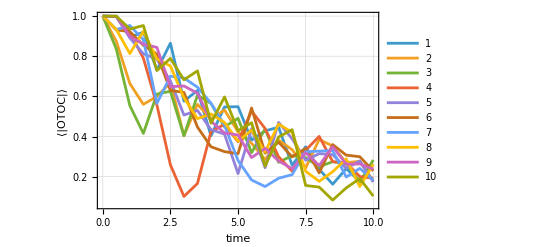

```mathematica
ListLinePlot[Array[otoc,$n],
DataRange->{0,$n},
PlotRange->All,
PlotLegends->Range[$n],
FrameLabel->{"time","⟨|OTOC|⟩"}
]
```

| Related Guides
▪Fermionic Quantum Computation

| Related Tech Notes
▪Quantum Computation: Overview
▪Quantum Information Systems with Q3
▪Q3: Quick Start

| Related Links
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).